```mathematica
ClearAll["Global`*"]
coordenadasU:={t,r,θ,ϕ,γ}
len:=Length[coordenadasU]
g={{-NN[r]^2*f[r],0,0,0,0},{0,1/f[r],0,0,0},{0,0,r^2,0,0},{0,0,0,r^2*Sin[θ]^2,0},{0,0,0,0,r^2*Sin[θ]^2*Sin[ϕ]^2}};
ginv=Inverse[g];
nn={{-1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}};
```

```mathematica
detg:=Assuming[NN[r]>0&&r>0&&Sin[θ]^4>0&&Sin[ϕ]>0,Simplify[Sqrt[-Det[g]]]]
r1={x[0]->t};
r2={x[1]->r};
r3={x[2]->θ};
r4={x[3]->ϕ};
r5={x[4]->γ};
```

### Definitions of g_(μ ν) , g^(μ ν)

```mathematica
For[j=0,j<len,j++,For[i=0,i<len,i++,gdown[i,j]=g⟦i+1⟧⟦j+1⟧;]]
For[j=0,j<len,j++,For[i=0,i<len,i++,gup[i,j]=ginv⟦i+1⟧⟦j+1⟧;]]
```

### Christoffel’s symbols → Γ_(μ ν)^ρ=Γ[ρ,μ,ν], la primera variable es la que es contravariante

```mathematica
ClearAll[μ,ν,ρ,σ]
For[μ=0,μ<len,μ++,
For[ν=0,ν<len,ν++,
For[ρ=0,ρ<len,ρ++,
Γ[ρ,μ,ν]=Series[1/2 *Sum[gup[ρ,σ] (D[gdown[ν,σ],x[μ]/.r1/.r2/.r3/.r4/.r5]+D[gdown[σ,μ],x[ν]/.r1/.r2/.r3/.r4/.r5]-D[gdown[μ,ν],x[σ]/.r1/.r2/.r3/.r4]/.r5),{σ,0,len-1}],{ϵ,0,2}];
]
]
]
```

### Riemann’s Tensor

```mathematica
ClearAll[μ,ν,ρ,σ,λ]
For[μ=0,μ<len,μ++,
For[ν=0,ν<len,ν++,
For[σ=0,σ<len,σ++,
For[ρ=0,ρ<len,ρ++,
RiemUDDD[ρ,σ,μ,ν]=Simplify[D[Γ[ρ,σ,ν],x[μ]/.r1/.r2/.r3/.r4/.r5]-D[Γ[ρ,σ,μ],x[ν]/.r1/.r2/.r3/.r4/.r5]+Sum[Γ[ρ,λ,μ]* Γ[λ,σ,ν],{λ,0,len-1}]-Sum[Γ[ρ,λ,ν]* Γ[λ,σ,μ],{λ,0,len-1}]];
]
]
]
]
ClearAll[μ,ν,ρ,σ,ψ]
For[μ=0,μ<len,μ++,
For[ν=0,ν<len,ν++,
For[σ=0,σ<len,σ++,
For[ρ=0,ρ<len,ρ++,
RiemDDDD[μ,ν,ρ,σ]=Sum[gdown[μ,ψ]*RiemUDDD[ψ,ν,ρ,σ],{ψ,0,len-1}]
]
]
]
]
ClearAll[μ,ν,ρ,σ,ψ]
For[μ=0,μ<len,μ++,
For[ν=0,ν<len,ν++,
For[σ=0,σ<len,σ++,
For[ρ=0,ρ<len,ρ++,
RiemUUUD[μ,ν,ρ,σ]=Sum[gdown[σ,ψ]*RiemUUUU[μ,ν,ρ,ψ],{ψ,0,len-1}]
]
]
]
]
ClearAll[μ,ν,ρ,σ,ψ]
For[μ=0,μ<len,μ++,
For[ν=0,ν<len,ν++,
For[σ=0,σ<len,σ++,
For[ρ=0,ρ<len,ρ++,
RiemDDDU[μ,ν,ρ,σ]=Sum[gup[σ,ψ]*RiemDDDD[μ,ν,ρ,ψ],{ψ,0,len-1}]
]
]
]
]
ClearAll[μ,ν,ρ,σ,λ]
For[μ=0,μ<len,μ++,
For[ν=0,ν<len,ν++,
For[σ=0,σ<len,σ++,
For[ρ=0,ρ<len,ρ++,
RiemUUUU[μ,ν,ρ,σ]=Sum[gup[σ,φ]*gup[ν,β]*gup[ρ,ψ]*RiemUDDD[μ,β,ψ,φ],{φ,0,len-1},{ψ,0,len-1},{β,0,len-1}]
]
]
]
]
ClearAll[μ,ν,ρ,σ,λ]
For[μ=0,μ<len,μ++,
For[ν=0,ν<len,ν++,
For[σ=0,σ<len,σ++,
For[ρ=0,ρ<len,ρ++,
RiemUUDD[μ,ν,ρ,σ]=Sum[gup[ν,ψ]*RiemUDDD[μ,ψ,ρ,σ],{ψ,0,len-1}]
]
]
]
]
ClearAll[μ,ν,ρ,σ,λ]
For[μ=0,μ<len,μ++,
For[ν=0,ν<len,ν++,
For[σ=0,σ<len,σ++,
For[ρ=0,ρ<len,ρ++,
RiemUDUD[μ,ν,ρ,σ]=Sum[gup[ρ,ψ]*RiemUDDD[μ,ν,ψ,σ],{ψ,0,len-1}]
]
]
]
]
```

### Ricci’s Tensor → R_(μ ν) = (R_(μ ρ ν))^ρ= Ric[μ,ν]

```mathematica
ClearAll[μ,ν,ρ,σ]
For[μ=0,μ<len,μ++,
For[ν=0,ν<len,ν++,
RDD[μ,ν]=Expand[Simplify[Sum[RiemDDDU[μ,ρ,ν,ρ],{ρ,0,len-1}]]];
]
]
ClearAll[μ,ν,ρ,σ]
For[μ=0,μ<len,μ++,
For[ν=0,ν<len,ν++,
RUU[μ,ν]=Expand[Simplify[Sum[gup[μ,α]*gup[ν,β]*RDD[α,β],{α,0,len-1},{β,0,len-1}]]];
]
]
ClearAll[μ,ν,ρ,σ]
For[μ=0,μ<len,μ++,
For[ν=0,ν<len,ν++,
RUD[μ,ν]=Expand[Simplify[Sum[gup[μ,α]*RDD[α,ν],{α,0,len-1}]]];
]
]
ClearAll[μ,ν,ρ,σ]
For[μ=0,μ<len,μ++,
For[ν=0,ν<len,ν++,
RDU[μ,ν]=Expand[Simplify[Sum[gup[ν,α]*RDD[μ,α],{α,0,len-1}]]];
]
]
```

### Scalar Ricci → R = R_(μ ν) g^(μ ν)

```mathematica
ClearAll[μ,ν]
R=Expand[Simplify[Sum[Sum[gup[μ,ν] RDD[μ,ν],{μ,0,len-1}],{ν,0,len-1}]]];
```

## Orden 1

### Densidad lagrangiana orden 1

```mathematica
L1:=R
```

```mathematica
Lagrange=Collect[Simplify[L1*detg/(Sin[θ]^2 Sin[ϕ])],{NN[r],NN'[r],NN''[r]}]
```

-r (6 r f[r]+3 r^2 f'[r]) NN'[r]-r NN[r] (-6+6 f[r]+6 r f'[r]+r^2 f''[r])-2 r^3 f[r] NN''[r]

### Verificiación GQTG

```mathematica
Lagrange1:=Lagrange/.NN[r]->1/.NN'[r]->0/.NN''[r]->0
D[Lagrange1,f[r]]-D[D[Lagrange1,f'[r]],r]+D[D[Lagrange1,f''[r]],{r,2}]
```

0

### Schwarzschild

```mathematica
exp1=Simplify[D[Lagrange,NN[r]]-D[D[Lagrange,NN'[r]],r]+D[D[Lagrange,NN''[r]],{r,2}]]==0
```

-3 r (-2+2 f[r]+r f'[r])==0

```mathematica
DSolve[exp1,f[r],r]
```

{{f[r]→1+C[1]/r^2}}

```mathematica
f1:=1-μ/(3r^2)
```

## Orden 2

### Invariantes de orden 2

```mathematica
I1:=Expand[R^2]
```

```mathematica
I2:=Simplify[Sum[RDD[μ,ν]*RUU[μ,ν],{μ,0,len-1},{ν,0,len-1}]]
```

```mathematica
I3=Simplify[Sum[RiemDDDD[μ,ν,σ,γ]*RiemUUUU[μ,ν,σ,γ],{μ,0,len-1},{ν,0,len-1},{σ,0,len-1},{γ,0,len-1}]]
```

1/(r^4 NN[r]^2)(9 r^4 f'[r]^2 NN'[r]^2+6 r^4 NN[r] f'[r] NN'[r] f''[r]+NN[r]^2 (12-24 f[r]+12 f[r]^2+6 r^2 f'[r]^2+r^4 f''[r]^2)+12 r^4 f[r] f'[r] NN'[r] NN''[r]+4 f[r] NN[r] (3 r^2 f'[r] NN'[r]+r^4 f''[r] NN''[r])+4 f[r]^2 (3 r^2 NN'[r]^2+r^4 NN''[r]^2))

### Densidad lagrangiana orden 2

```mathematica
L2:=Simplify[a*I1+b*I2+c*I3]
```

```mathematica
Collect[L2*detg/(Sin[θ]^2 Sin[ϕ]),{NN[r],NN'[r],NN''[r]}]
```

1/(2 r)NN[r] (72 a+24 b+24 c+24 (3 a+b+c) f[r]^2+3 (24 a+5 b+4 c) r^2 f'[r]^2-24 a r^2 f''[r]+2 a r^4 f''[r]^2+b r^4 f''[r]^2+2 c r^4 f''[r]^2+24 f[r] (-2 (3 a+b+c)+(6 a+b) r f'[r]+a r^2 f''[r])+6 r f'[r] (-4 (6 a+b)+(4 a+b) r^2 f''[r]))+1/(2 r)NN'[r] (24 (6 a+b) r f[r]^2+6 r f[r] (-4 (6 a+b)+(36 a+5 b+4 c) r f'[r]+(4 a+b) r^2 f''[r])+6 r^2 f'[r] (-12 a+3 (4 a+b) r f'[r]+(2 a+b+2 c) r^2 f''[r]))+1/(2 r)(48 a r^2 f[r]^2+4 r^2 f[r] (-12 a+3 (4 a+b) r f'[r]+(2 a+b+2 c) r^2 f''[r])) NN''[r]+1/NN[r](1/(2 r)(24 (3 a+b+c) r^2 f[r]^2+18 (4 a+b) r^3 f[r] f'[r]+9 (2 a+b+2 c) r^4 f'[r]^2) NN'[r]^2+((12 (4 a+b) r^3 f[r]^2+12 (2 a+b+2 c) r^4 f[r] f'[r]) NN'[r] NN''[r])/(2 r)+2 (2 a+b+2 c) r^3 f[r]^2 NN''[r]^2)

### Determinar a, b y c

```mathematica
L=Simplify[(L1+L2)*detg/(Sin[θ]^2 Sin[ϕ])]
```

6 r NN[r]-6 r f[r] NN[r]-6 r^2 NN[r] f'[r]-6 r^2 f[r] NN'[r]-3 r^3 f'[r] NN'[r]-r^3 NN[r] f''[r]+3 r f'[r] NN'[r] (-12 a+3 (4 a+b) r f'[r]+(2 a+b+2 c) r^2 f''[r])+1/(2 r)NN[r] (72 a+24 b+24 c+24 (3 a+b+c) f[r]^2+3 (24 a+5 b+4 c) r^2 f'[r]^2-24 a r^2 f''[r]+2 a r^4 f''[r]^2+b r^4 f''[r]^2+2 c r^4 f''[r]^2+24 f[r] (-2 (3 a+b+c)+(6 a+b) r f'[r]+a r^2 f''[r])+6 r f'[r] (-4 (6 a+b)+(4 a+b) r^2 f''[r]))-2 r^3 f[r] NN''[r]+12 f[r]^2 ((6 a+b) NN'[r]+2 a r NN''[r])+f[r] (3 NN'[r] (-4 (6 a+b)+(36 a+5 b+4 c) r f'[r]+(4 a+b) r^2 f''[r])+2 r (-12 a+3 (4 a+b) r f'[r]+(2 a+b+2 c) r^2 f''[r]) NN''[r])+1/(2 NN[r])r (9 (2 a+b+2 c) r^2 f'[r]^2 NN'[r]^2+6 r f[r] f'[r] NN'[r] (3 (4 a+b) NN'[r]+2 (2 a+b+2 c) r NN''[r])+4 f[r]^2 (6 (3 a+b+c) NN'[r]^2+3 (4 a+b) r NN'[r] NN''[r]+(2 a+b+2 c) r^2 NN''[r]^2))

```mathematica
L1f=L/.NN[r]->1/.NN'[r]->0/.NN''[r]->0
```

6 r-6 r f[r]-6 r^2 f'[r]-r^3 f''[r]+1/(2 r)(72 a+24 b+24 c+24 (3 a+b+c) f[r]^2+3 (24 a+5 b+4 c) r^2 f'[r]^2-24 a r^2 f''[r]+2 a r^4 f''[r]^2+b r^4 f''[r]^2+2 c r^4 f''[r]^2+24 f[r] (-2 (3 a+b+c)+(6 a+b) r f'[r]+a r^2 f''[r])+6 r f'[r] (-4 (6 a+b)+(4 a+b) r^2 f''[r]))

```mathematica
exp=Collect[Simplify[D[L1f,f[r]]-D[D[L1f,f'[r]],r]+D[D[L1f,f''[r]],{r,2}]],{f[r],f'[r],f''[r],f'''[r],f''''[r]}]
```

(-72 a-24 b-24 c)/r+(24 (3 a+b+c) f[r])/r-3 (8 a+3 b+4 c) f'[r]+((-12 a r^2-3 b r^2) f''[r])/r+((12 a r^3+6 b r^3+12 c r^3) f^(3)[r])/r+((2 a r^4+b r^4+2 c r^4) f^(4)[r])/r

```mathematica
Solve[{Coefficient[exp,f[r]]==0,Coefficient[exp,f'[r]]==0,Coefficient[exp,f''[r]]==0,Coefficient[exp,f'''[r]]==0,Coefficient[exp,f''''[r]]==0},{a,b,c}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{b→-4 a,c→a}}

### Solución Gauss Bonnet

```mathematica
Clear[α]
```

```mathematica
a:=α/6
b:=-4*a
c:=a
```

```mathematica
Collect[L,{NN[r],NN'[r],NN''[r]}]
```

(-6 r^2 f[r]+4 α f[r]^2-3 r^3 f'[r]-6 r α f'[r]+3 f[r] (-(4 α)/3+10/3 r α f'[r])) NN'[r]+NN[r] (6 r-6 r f[r]-6 r^2 f'[r]-r^3 f''[r]+1/(2 r)(-8 r α f'[r]+4 r^2 α f'[r]^2-4 r^2 α f''[r]+24 f[r] (1/3 r α f'[r]+1/6 r^2 α f''[r])))+(-2 r^3 f[r]-4 r α f[r]+4 r α f[r]^2) NN''[r]

```mathematica
Expand[-6 r^2 f[r]+4 α f[r]^2-3 r^3 f'[r]-6 r α f'[r]+3 f[r] (-(4 α)/3+10/3 r α f'[r])]
```

-6 r^2 f[r]-4 α f[r]+4 α f[r]^2-3 r^3 f'[r]-6 r α f'[r]+10 r α f[r] f'[r]

```mathematica
exp2=Simplify[Expand[D[L,NN[r]]-D[D[L,NN'[r]],r]+D[D[L,NN''[r]],{r,2}]]]==0
```

6 r-(3 r^2+2 α) f'[r]+f[r] (-6 r+2 α f'[r])==0

```mathematica
Expand[Simplify[DSolve[exp2,f[r],r]]]
```

{{f[r]→1+(3 r^2)/(2 α)+1/2 √(-1/α) √(-(9 r^4)/α-4 α (1+C[1]))},{f[r]→1+(3 r^2)/(2 α)-1/2 √(-1/α) √(-(9 r^4)/α-4 α (1+C[1]))}}

```mathematica
f2=FullSimplify[1+(3 r^2)/(2 α)+1/2 √(-1/α) √(-(9 r^4)/α-4 α (1+c1))]
```

1/2 (2+(3 r^2)/α+√(-1/α) √(-(9 r^4)/α-4 (1+c1) α))

```mathematica
f21:=1+r^2/(4 α)+(√(r^4/α+8 μ))/(4 √α)
```

```mathematica
f22:=1+r^2/(4 α)-(√(r^4/α+8 μ))/(4 √α)
```

## Gráfica

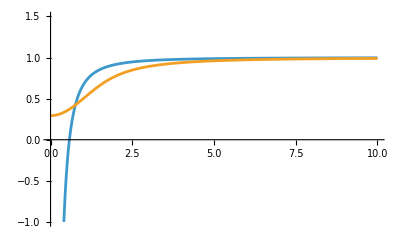

```mathematica
α:=1
μ:=1
Plot[{f1,f22},{r,0,10},PlotRange->{-1,1.5}]
```

### M.08étodo GQTG

```mathematica
Lf=Expand[L/.NN[r]->1/.NN'[r]->0/.NN''[r]->0]
```

6 r-6 r f[r]-6 r^2 f'[r]-4 α f'[r]+4 α f[r] f'[r]+2 r α f'[r]^2-r^3 f''[r]-2 r α f''[r]+2 r α f[r] f''[r]

```mathematica
Simplify[Expand[D[Lf,f[r]]-D[D[Lf,f'[r]],r]+D[D[Lf,f''[r]],{r,2}]]]==0
```

True

```mathematica
F0'[r_]=Coefficient[L,NN[r]]
F1[r_]=Coefficient[L,NN'[r]]
F2[r_]=Coefficient[L,NN''[r]]
```

6 r-6 r f[r]-6 r^2 f'[r]-r^3 f''[r]+1/(2 r)(-8 r α f'[r]+4 r^2 α f'[r]^2-4 r^2 α f''[r]+24 f[r] (1/3 r α f'[r]+1/6 r^2 α f''[r]))

-6 r^2 f[r]-4 α f[r]+4 α f[r]^2-3 r^3 f'[r]-6 r α f'[r]+10 r α f[r] f'[r]

-2 r^3 f[r]-4 r α f[r]+4 r α f[r]^2

```mathematica
Simplify[Integrate[F0'[r],r]-F1[r]+D[F2[r],r]]
```

3 r^2-(3 r^2+2 α) f[r]+α f[r]^2

```mathematica
Expand[Solve[3 r^2-(3 r^2+2 α) f[r]+α f[r]^2==c2,f[r]]]
```

{{f[r]→1+(3 r^2)/(2 α)-(√(9 r^4+4 c2 α+4 α^2))/(2 α)},{f[r]→1+(3 r^2)/(2 α)+(√(9 r^4+4 c2 α+4 α^2))/(2 α)}}